```mathematica
FindMinEdges5[g_]:=Block[{minChrom=Null,min=Null,global=ChromaticPolynomial[g,4],removed,chrom,form},
Table[
removed=EdgeDelete[g,e];
chrom=ChromaticPolynomial[removed,4];
If[minChrom==Null, 
minChrom=chrom;
min={},
If[chrom<minChrom,
minChrom=chrom;
min={}
]];
If[chrom==minChrom,AppendTo[min,e]];
,{e, EdgeList[g]}
];
form=FindEmptyFormula[g];
min=Table[e<->Graph[g,GraphHighlight->e,VertexLabels->"Name",GraphLayout->"PlanarEmbedding"]<->Graph[FormulaGraphReverse2[ListofVars[form]],GraphHighlight->With[{temp=FormulaGraphReverse2[ListofVars[FindEmptyFormula[EdgeDelete[g,e]]]]},Join[VertexList[temp],EdgeList[temp]]],ImageSize->800],{e,Take[min,1]}];
{global,minChrom,min}
]
```

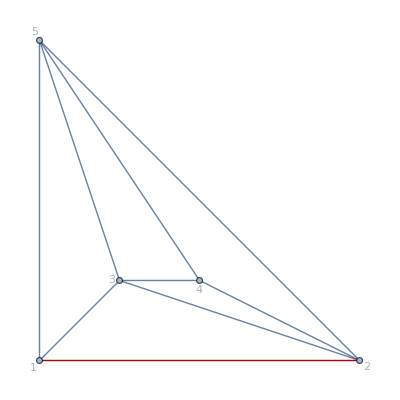
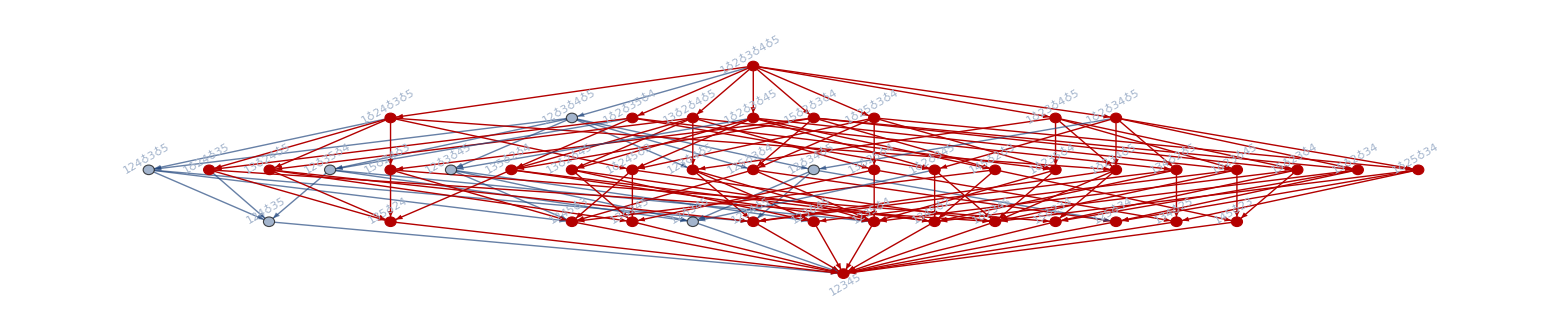
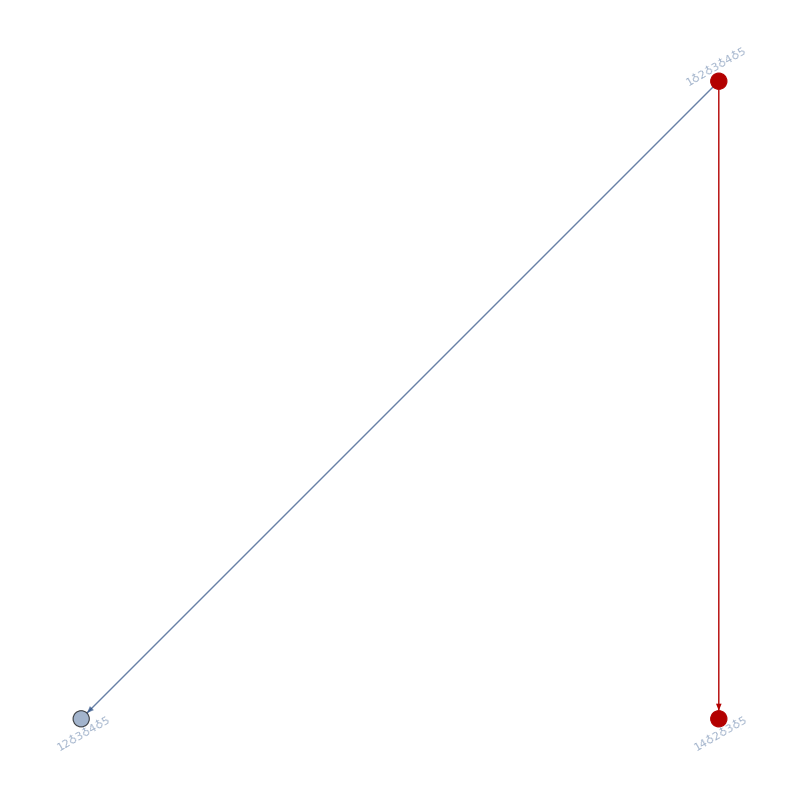
2 | 24 | 48 | {1<->2<->-Graphics-<->-Graphics-} | 24 | 48 | {1<->2<->-Graphics-<->-Graphics-}

```mathematica
Monitor[TableForm[Table[With[{g=ReadGrof[k]},Join[Prepend[FindMinEdges5[g],k],FindMinEdges4[g]]],{k,2,2}],TableDepth->3],{k,e}]
```

```mathematica
FindMinEdges6[g_]:=Block[{minChrom=Null,min=Null,global=ChromaticPolynomial[g,4],removed,chrom,form},
Table[
removed=EdgeDelete[g,e];
chrom=ChromaticPolynomial[removed,4];
If[minChrom==Null, 
minChrom=chrom;
min={},
If[chrom<minChrom,
minChrom=chrom;
min={}
]];
If[chrom==minChrom,AppendTo[min,e]];
,{e, EdgeList[g]}
];
form=FindFullFormula[g];
min=Table[e<->Graph[g,GraphHighlight->e,VertexLabels->"Name",GraphLayout->"PlanarEmbedding"]<->Graph[FormulaGraphReverse2[SetDifference[ListofVars[FindFullFormula[EdgeDelete[g,e]]],ListofVars[form]]],ImageSize->600]<->Graph[EdgeContract[g,e],GraphHighlight->e,VertexLabels->"Name",GraphLayout->"PlanarEmbedding"]<->Labeled[Graph[FormulaGraphReverse2[FindFullFormula[EdgeContract[g,e]]],ImageSize->600],Style[e,Red]],{e,Take[min,1]}];
{global,minChrom,min}
]
```

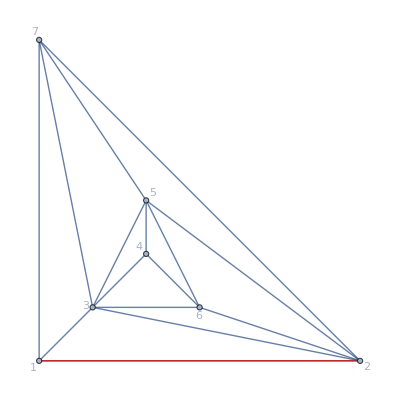
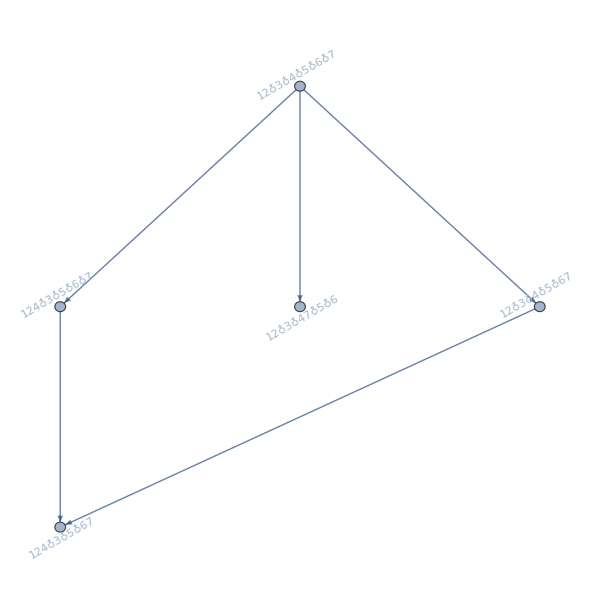
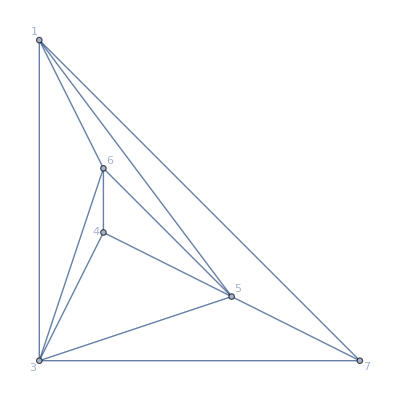
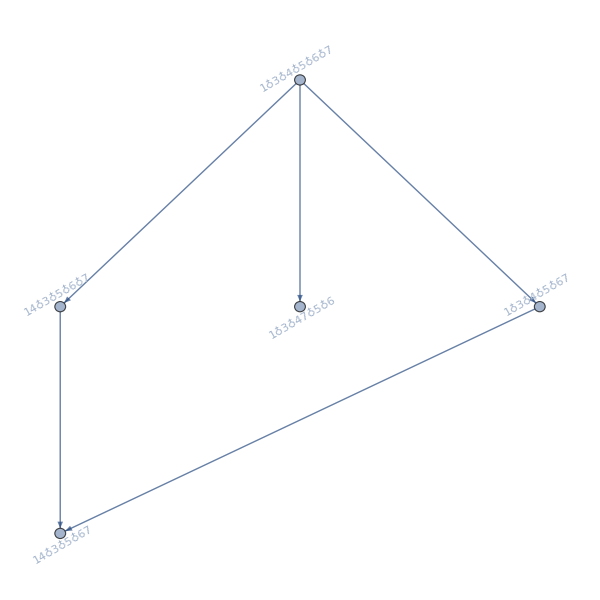
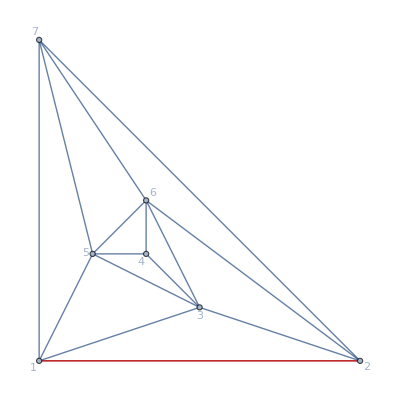
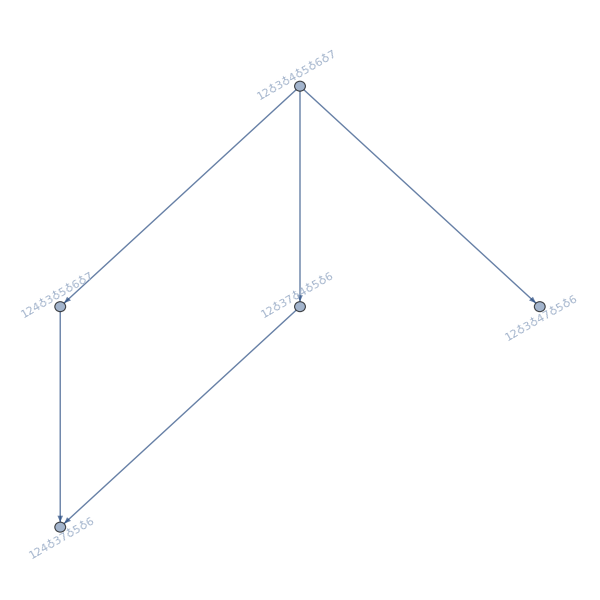
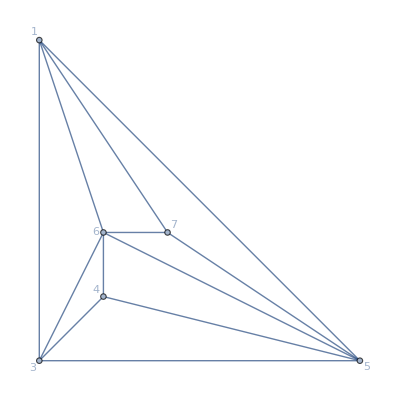
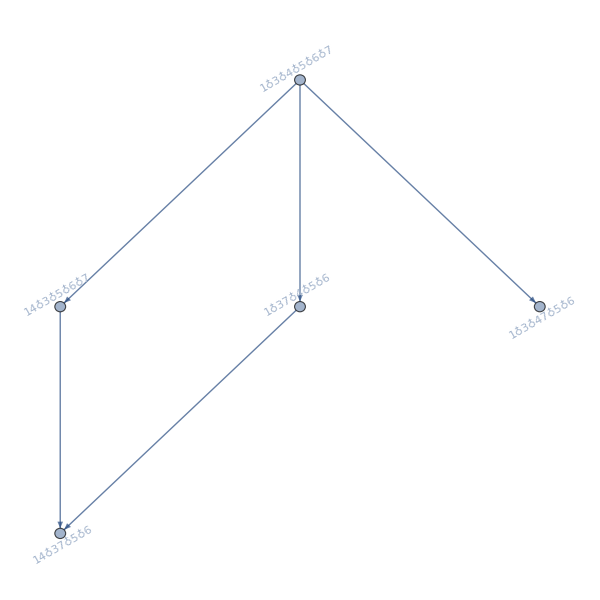
5 | 24 | 48 | {1<->2<->-Graphics-<->-Graphics-<->-Graphics-<->-Graphics-1<->2}
6 | 96 | 120 | {1<->2<->-Graphics-<->-Graphics-<->-Graphics-<->-Graphics-1<->2}
7 | 120 | 216 | {1<->2<->-Graphics-<->-Graphics-<->-Graphics-<->-Graphics-1<->2}
8 | 24 | 48 | {1<->2<->-Graphics-<->-Graphics-<->-Graphics-<->-Graphics-1<->2}
9 | 24 | 48 | {1<->2<->-Graphics-<->-Graphics-<->-Graphics-<->-Graphics-1<->2}
10 | 24 | 48 | {1<->2<->-Graphics-<->-Graphics-<->-Graphics-<->-Graphics-1<->2}

```mathematica
Monitor[TableForm[Table[With[{g=ReadGrof[k]},Prepend[FindMinEdges6[g],k]],{k,5,10}],TableDepth->3],{k,e}]
```

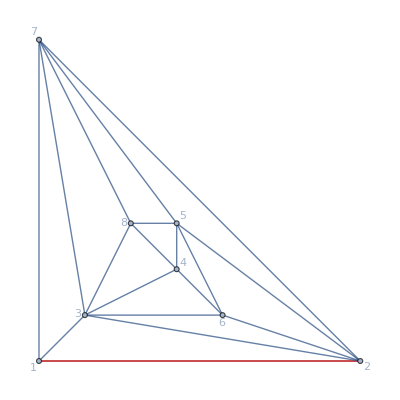
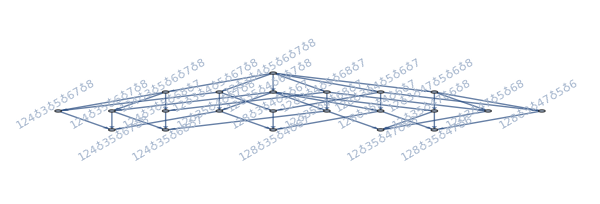
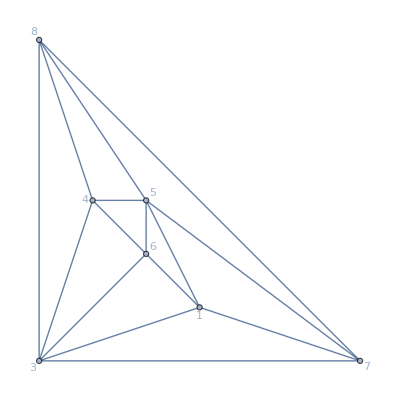
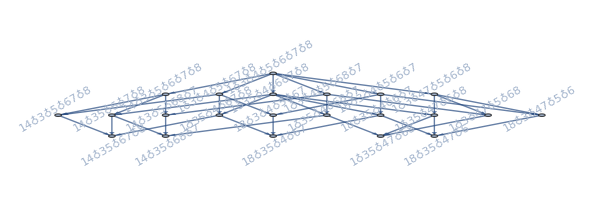
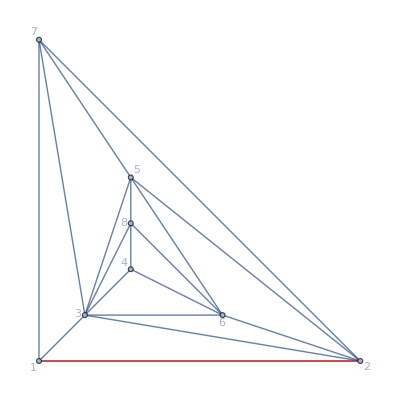
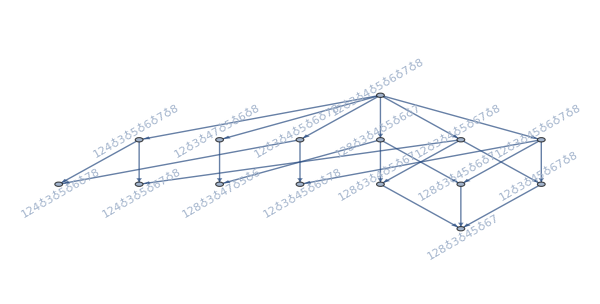
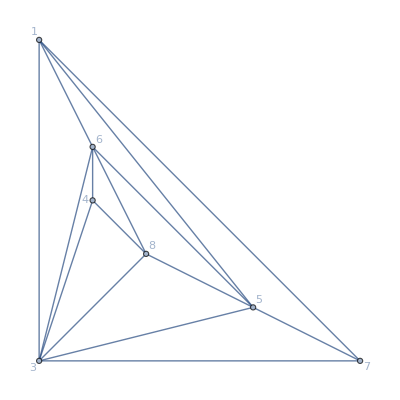
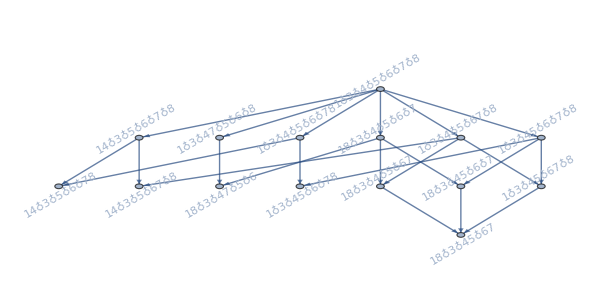
7 11 | 120 | 240 | {1<->2<->-Graphics-<->-Graphics-<->-Graphics-<->-Graphics-1<->2}
12 | 24 | 48 | {1<->2<->-Graphics-<->-Graphics-<->-Graphics-<->-Graphics-1<->2}
13 | 24 | 48 | {1<->2<->-Graphics-<->-Graphics-<->-Graphics-<->-Graphics-1<->2}
14 | 96 | 192 | {1<->2<->-Graphics-<->-Graphics-<->-Graphics-<->-Graphics-1<->2}
15 | 96 | 192 | {1<->2<->-Graphics-<->-Graphics-<->-Graphics-<->-Graphics-1<->2}

```mathematica
Monitor[TableForm[Table[With[{g=ReadGrof[k]},Prepend[FindMinEdges6[g],k]],{k,11,15}],TableDepth->3],{k,e}]7
```